# Linear algebra with Mathematica

Notes on linear algebra.

## 1. Learning the toolset

## Vectors

Lists are vectors

```mathematica
{1, 2, 3}
```

{1,2,3}

Use "VectorQ" to check if something is a vector.

```mathematica
VectorQ @ {1, 2, 3}
```

True

Operations work element-wise.

```mathematica
{1, 2, 3} + {1, 0, 1}
```

{2,2,4}

```mathematica
{1, 2, 3} * 11
```

{11,22,33}

```mathematica
√{4, 9, 121}
```

{2,3,11}

```mathematica
x^{1, 2, 3} - 9
```

{-9+x,-9+x^2,-9+x^3}

```mathematica
D[x^{1, 2, 3} - 9, x]
```

{1,2 x,3 x^2}

Dot product and cross product.

```mathematica
v = {a, b, c} ;
u={d, e, f} ;
```

```mathematica
v.u
```

a d+b e+c f

```mathematica
v×u
```

{-c e+b f,c d-a f,-b d+a e}

```mathematica
Norm[v]
```

√(Abs[a]^2+Abs[b]^2+Abs[c]^2)

```mathematica
{{1, 2, 3} , {2, 4, 9}}// TableForm
```

1 | 2 | 3
2 | 4 | 9

## Matrices

Matrices are lists of lists and will appear that way unless a transformation is applied.

```mathematica
{{1, 2}, {3, 4}}
```

{{1,2},{3,4}}

Using MatrixForm to display matrices ruins the "chaining" of computations. It is better to use the $Post global variable to apply only a visual transformation.

```mathematica
$Post := If[MatrixQ[#], MatrixForm[#], #] &
```

```mathematica
MatrixForm[{{1, 2}, {3, 4}}]* 2 
(*Multiplication Fails*)
```

2 (1 | 2
3 | 4)

```mathematica
{{a, b}, {"cat", 1}}
(*No type checking—symbolic*)
```

{{a,b},{cat,1}}

How to generate random matrices for examples, etc.

```mathematica
RandomChoice[{"apple", "orange", "taco"}, {4, 4}]
```

(apple | apple | taco | apple
taco | orange | orange | taco
apple | taco | orange | apple
taco | apple | apple | apple)

Plot a matrix

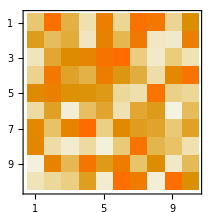

```mathematica
RandomInteger[{0, 999}, {10, 10}] // MatrixPlot
```

Check if something is a matrix

```mathematica
MatrixQ @ {{1, 1}, {1, 1}}
```

True

Table of random values is a matrix.

```mathematica
MatrixQ @ Table[RandomVariate[NormalDistribution[], 10],10]
```

True

Multiply a matrix by its inverse to get an identity matrix.

```mathematica
Inverse [ {{1, 2}, {3, 4}} ].  {{1,2}, {3,4}} // TableForm
```

1 | 0
0 | 1

```mathematica
RandomInteger[{0, 100}, {10, 10}] //MatrixForm
```

(82 | 62 | 1 | 35 | 78 | 80 | 11 | 89 | 50 | 10
44 | 77 | 90 | 10 | 7 | 42 | 57 | 38 | 44 | 5
84 | 42 | 40 | 57 | 96 | 21 | 90 | 70 | 21 | 12
36 | 15 | 5 | 25 | 59 | 92 | 49 | 80 | 19 | 75
20 | 64 | 14 | 36 | 76 | 3 | 7 | 29 | 74 | 53
87 | 79 | 3 | 20 | 8 | 67 | 46 | 46 | 62 | 34
61 | 53 | 59 | 93 | 0 | 66 | 79 | 75 | 23 | 70
69 | 71 | 57 | 36 | 67 | 84 | 88 | 56 | 52 | 56
14 | 30 | 18 | 66 | 2 | 0 | 83 | 67 | 52 | 49
98 | 7 | 21 | 71 | 84 | 74 | 80 | 33 | 69 | 23)

## 2. Basic linear algebra

## Eigenvalues, etc.

### The basics

A key expression in finding eigenvalues and eigenspaces is A - λI

```mathematica
A = {{1, 2}, {4, 3}};
identity = IdentityMatrix[2];
```

Setting the determinant equal to zero gives the characteristic function.

```mathematica
Det[A - λ*identity ] == 0
```

-5-4 λ+λ^2==0

```mathematica
CharacteristicPolynomial[A, λ]
```

-5-4 λ+λ^2

The function can then be solved to get the eigenvalues

```mathematica
eigenvalues = Det[A- λ*identity ] == 0 // Solve
```

(λ→-1
λ→5)

```mathematica
Eigenvalues[A ]
```

{5,-1}

Now that we have our eigenvalues, we can solve for the null space of the expression, which will give the eigenspace.

```mathematica
NullSpace /@ ( A - λ*identity /. eigenvalues)
```

{{{-1,1}},{{1,2}}}

```mathematica
Eigenvectors[A]
```

{{1,2},{-1,1}}

### Similarity

Two matrices are said to be similar if . If two matrices are similar, they also have the same eigenvalues (but not the same eigenvectors—which would make them the same matrix). This can be proved easily.

### ?

For an  matrix ... the number of unique eigenvalues tells us interesting information about the properties of a system / transformation.

An identity matrix only has a single eigenvalue.

```mathematica
CharacteristicPolynomial[IdentityMatrix[6], λ]
IdentityMatrix[6] // Eigenvalues
```

1-6 λ+15 λ^2-20 λ^3+15 λ^4-6 λ^5+λ^6

{1,1,1,1,1,1}

```mathematica
Eigenvalues[{{1,2,3}, {2, 4, 6}, {1, 6, 7}}]
```

{2 (3+√10),2 (3-√10),0}

#### Diagonal matrices

```mathematica
RandomInteger[{0, 99}, {3, 3}]  // Eigenvalues // N
```

{169.506,66.7329,-51.2389}

If an n x n matrix is diagonalizable, then it has n unique eigenvalues.

```mathematica
DiagonalizableMatrixQ @ Identity[10]
```

False

It’s very difficult to generate a random matrix that is not diagonalizable.

```mathematica
Table[DiagonalizableMatrixQ @ RandomInteger[{0, 99}, {2, 2}], 100] // Counts
```

<|True→100|>

## Solving systems of equations

Three ways to go about doings this: (a) directly using systems of equations, (b) keeping the coefficients and right hand side separate and using LinearSolve, and (c) joining both sides and using RowReduce.

```mathematica
A ={{1, -2, 1}, {0, 2, -8}, {-4, 5, 9}};
b = {0, 8, -9};
LinearSolve[A, b]
```

{29,16,3}

```mathematica
RowReduce @MapThread[Append, {A, b}]
```

(1 | 0 | 0 | 29
0 | 1 | 0 | 16
0 | 0 | 1 | 3)

## Bits and pieces

### Adjacent matrices from a graph

Generate a random graph with 20 vertices and 50 edges

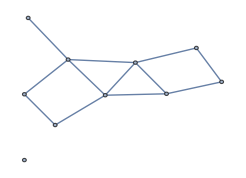

```mathematica
g = RandomGraph[{10,12}]
```

Get its adjacency matrix

```mathematica
AdjacencyMatrix[g] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)

Count the number of connections (edges). You need to divide by two.

```mathematica
g // AdjacencyMatrix // Flatten // Total // Divide[#, 2] &
```

12

Note that we would get the "correct" number of edges wit ha directed graph.

```mathematica
RandomGraph[{10, 12}, DirectedEdges -> True] // EdgeList //Length
```

12

### Random transformations on a cube

Applying random transformation matrices. May be useful later when looking at a collapse applied to an object.

```mathematica
Graphics3D[#, Boxed->False]& /@ 
Table[
{{Opacity[.35], Blue, gr},
GeometricTransformation[{Opacity[.85], Orange , gr}, 
						{RandomReal[{-1, 1}, {3, 3}], {0, 0, 0}}] }, 
6]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Applying identity (with slight jitter)

```mathematica
Graphics3D[#, Boxed->False]& @ 
{{Opacity[.5], Yellow, gr},
GeometricTransformation[{Opacity[.5],Blue , gr}, 
						{IdentityMatrix[3], {0, 0.01, 0}}] }
```

-Graphics3D-

Trying to collapse:

```mathematica
Manipulate[
Graphics3D[#, Boxed->False]& @ 
{{Opacity[.2], White, gr},
GeometricTransformation[{Red , gr}, 
						{{{.1, .2, .3},{x,y, z}, {.7, .7, .7}}, {0, 0, 0}}] },
{x, -1, 1}, {y, -1, 1}, {z, -1, 1}]
```